Forward kinematics of 3-link planar robot arm
Keitaro Naruse
University of Aizu, Japan

```mathematica
(*Robot arm parameters*)
(*Link length*)
L1=1;L2=1;L3=1;
```

```mathematica
(*Forward kinematics function defined in FK[]*)
(*Input: q: a vector of three joint angles, {q1=q[[1]], q2=q[[2]], q3=q[[3]]*)
(*Output: p: a vector of four joint poses, {p1=p[[1]], p2=p[[2]], p3=p[[3]], p4=p[[4]]}*)
(*p1: first joint = base*)
(*p2: second joint = end of the first link*)
(*p3: third joint = end of the second link*)
(*p4: hand tip = end of the last link*)
(*p1, p2, p3, p4 is a vector of {x,y,q}, x-coordinae, y-coordinae, and angle*)
FK[q_]:=
Module[{p1, p2, p3, p4},
p1 = {0,0,0};
p2 = p1+{L1 Cos[q[[1]]],L1 Sin[q[[1]]],q[[1]]};
p3 = p2+{L2 Cos[q[[1]]+q[[2]]],L2 Sin[q[[1]]+q[[2]]],q[[2]]};
p4 = p3+{L3 Cos[q[[1]]+q[[2]]+q[[3]]],L3 Sin[q[[1]]+q[[2]]+q[[3]]],q[[3]]};
{p1,p2, p3, p4}
];
```

```mathematica
(*Instance of a joint angle set*)
(*A vector of three joint angles represented in [rad]*)
q={0.1, 0.4, 0.9};
```

```mathematica
(*Instance of forward kinematics calculation*)
(*It returns four poses of (x,y,q)*)
p = FK[q]
```

{{0,0,0},{0.995004,0.0998334,0.1},{1.87259,0.579259,0.5},{2.04255,1.56471,1.4}}

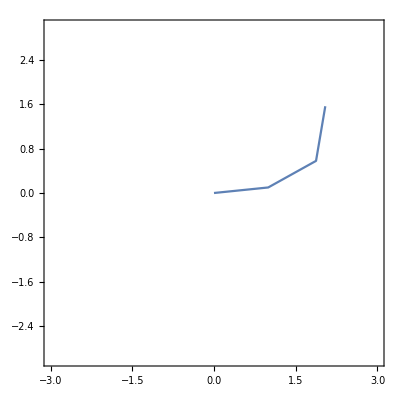

```mathematica
(*Draw a robot arm*)
(*We plot the four joints position connecting with a line as a robot arm pose by ListPlot[]*)
(*We need only the first two componet of the poses (x,y,q) for plotting a robot pose*)
(*p[[i,1;;2]] represents the first and second element of the i-th element of p*)
ListPlot[{p[[1,1;;2]], p[[2,1;;2]], p[[3,1;;2]], p[[4,1;;2]]},
Joined->True,
PlotRange->{{-3,3},{-3,3}},
Frame->True,
AspectRatio->1]
```

```mathematica
(*Give an interactive interface by Minipulate[]*)
(*q1, q2, q3 are controlled in the interface*)
Manipulate[
(*Give an angle set from the interface*)
q={q1,q2,q3};
(*Calculate forward kinematics*)
p = FK[q];
(*Draw a robot arm *)
ListPlot[{p[[1,1;;2]], p[[2,1;;2]], p[[3,1;;2]], p[[4,1;;2]]},
Joined->True,
PlotRange->{{-3,3},{-3,3}},
Frame->True,
AspectRatio->1],
{{q1,0},-π,π},{{q2,0},-π,π},{{q3,0},-π,π}
]
```